## MNIST dataset

```mathematica
trainingData = ResourceData["MNIST", "TrainingData"];
testData = ResourceData["MNIST", "TestData"];
```

```mathematica
RandomSample[trainingData,5]
```

{-Graphics-→0,-Graphics-→9,-Graphics-→9,-Graphics-→7,-Graphics-→6}

```mathematica
encoder = NetEncoder[{"Image", {28,28}, "ColorSpace"->"Grayscale"}]
```

NetEncoder[<>]

```mathematica
decoder = NetDecoder[{"Class", Range[0,9]}]
```

NetDecoder[<>]

```mathematica
newNet = NetChain[{
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[50,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
FlattenLayer[],
LinearLayer[500],
ElementwiseLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]
},
"Input"->encoder,
"Output"->decoder
]
```

NetChain[<>]

```mathematica
initNet=NetInitialize[newNet]
```

NetChain[<>]

```mathematica
trainingNet=NetGraph[<|
"net"->initNet,
"loss"->CrossEntropyLossLayer["Index"]|>,
{NetPort["Input"]->"net"->NetPort["loss", "Input"],
NetPort["Target"]->NetPort["loss", "Target"]}
]
```

NetGraph[<>]

```mathematica
sampleData=RandomSample[trainingData,5]
```

{-Graphics-→4,-Graphics-→7,-Graphics-→3,-Graphics-→4,-Graphics-→9}

```mathematica
inputSample=First/@sampleData
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
targetSample=Last/@sampleData
```

{4,7,3,4,9}

```mathematica
trainingNet[<|"Input"->inputSample,"Target"->targetSample|>]
```

{3.12465,4.07518,4.33475,2.93305,1.23455}

```mathematica
trainAssoc=<|"Input"->Keys[trainingData],
"Target"->Values[trainingData]+1|>;
testAssoc=<|"Input"->Keys[testData],"Target"->Values[testData]+1|>;
```

```mathematica
results=NetTrain[
trainingNet,trainAssoc,All,
ValidationSet->testAssoc,
MaxTrainingRounds->5
]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2814  rounds:3  time:2.4min  examples/s:1251
data | ,,  training examples:60000  validation examples:10000  processed examples:180096  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.14×10^-2  error:0.976%
validation | ,,  loss:3.43×10^-2  error:1.10%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
trainedNet=NetExtract[results["TrainedNet"], "net"]
```

NetChain[<>]

```mathematica
trainedNet=NetReplacePart[trainedNet,
{"Input"->encoder,"Output"->decoder}]
```

NetChain[<>]

```mathematica
First@inputSample
```

-Graphics-

```mathematica
trainedNet@%
```

4

```mathematica
trainedNet[-Graphics-, "TopProbabilities"]
```

{8→0.465067,2→0.260113,3→0.151437,9→0.0730793}

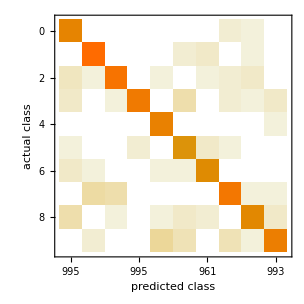
Classifier Measurements
Classifier method | Net
Number of test examples | 10000
Accuracy | (98.900.10) %
Accuracy baseline | (11.350.32) %
Geometric mean of probabilities | 0.966 ± 0.0026
Mean cross entropy | 0.0343 ± 0.0027
Single evaluation time | 3.05 ms/example
Batch evaluation speed | 3.67 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[trainedNet,testData]
```

```mathematica
measurements["WorstClassifiedExamples"]
```

{-Graphics-→6,-Graphics-→6,-Graphics-→5,-Graphics-→1,-Graphics-→7,-Graphics-→0,-Graphics-→7,-Graphics-→9,-Graphics-→9,-Graphics-→8}

```mathematica
measurements["TopConfusions"]
```

{3→5,1→6,2→8,3→9,5→6,8→9,0→7,1→5,2→7,3→7}